```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["test.txt","Table"];
cx=data⟦1;;(Length@data+1)/3⟧;
cy=data⟦(Length@data+1)/3+1;;(Length@data+1)/3*2⟧;
h=data⟦(Length@data+1)2/3+1;;-1⟧;
Length@data;
```

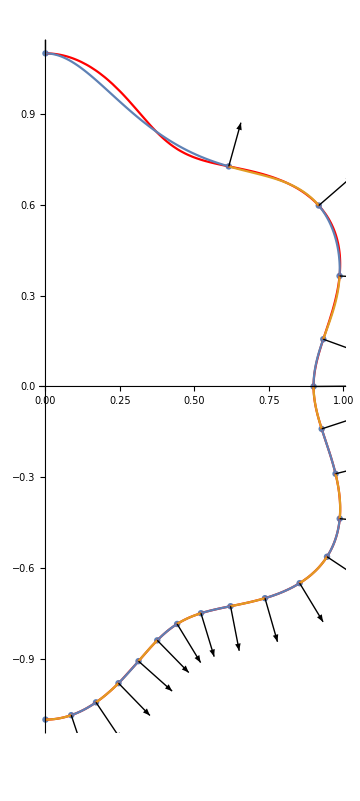

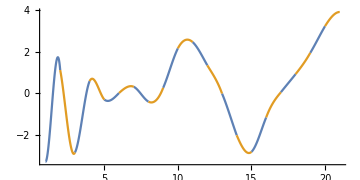

```mathematica
Subscript[sx, i_][t_]:=SetPrecision[cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5),15]
Subscript[sy, i_][t_]:=SetPrecision[cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5),15]
p[θ_]=(1+0.1Cos[6θ]){Sin[θ],Cos[θ]};
ar=Table[Arrow[{{Subscript[sx, i][0],Subscript[sy, i][0]},{Subscript[sx, i][0],Subscript[sy, i][0]}+0.15Normalize@{-Subscript[sy, i]'[0],Subscript[sx, i]'[0]}}],{i,1,Length@cx-1}];
Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,Length@cx-1}];
Show[ListPlot[Transpose[{cx⟦All,1⟧,cy⟦All,1⟧}]],ParametricPlot[p[θ],{θ,0,π},PlotStyle->Red],
ParametricPlot[{%⟦1;;-1;;2⟧,%⟦2;;-1;;2⟧},{t,0,1}],
Graphics[{ar}],AspectRatio->Automatic,ImageSize->Medium]
Table[{t+i,Subscript[sy, i]''[t]/h⟦i⟧^2},{i,1,Length@cx-1}];
Show[
ParametricPlot[{%⟦1;;-1;;2⟧,%⟦2;;-1;;2⟧},{t,0,1},AspectRatio->Automatic,PlotRange->All]
,AspectRatio->0.5]
```

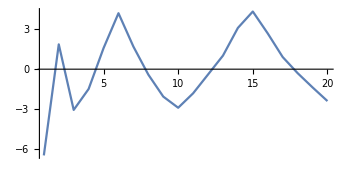

```mathematica
Clear[i,kv]
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5
ParallelTable[{0+i,Subscript[kv, i][0]+1},{i,1,Length@cx-1}];
Show[
ListPlot[%,PlotRange->All,Joined->True],AspectRatio->0.5]
```

```mathematica
i=2;
j=2;
{r,z}={Subscript[sx, i][t],Subscript[sy, i][t]};
{rp,zp}={Subscript[sx, j][t],Subscript[sy, j][t]}/.t->0;
{dr,dz}={Subscript[sx, i]'[t],Subscript[sy, i]'[t]};
J=√(dr^2+dz^2);
arc=NIntegrate[J,{t,0,1},PrecisionGoal->15,WorkingPrecision->15];
xi[g_?NumberQ]:=NIntegrate[J,{t,0,g},PrecisionGoal->15]/arc
a=rp^2+r^2+(zp-z)^2;
b=2 rp r;
m=2 b/(a+b);
eE=EllipticE[m];
eK=EllipticK[m];
N0=(1-xi[t])(1-2xi[t]) ;
N1=4(xi[t])(1-xi[t]) ;
N2=(xi[t])(2xi[t]-1) ;
SetOptions[NIntegrate,WorkingPrecision->14,PrecisionGoal->5];
NIntegrate[(r  J)/(π √(a+b))N0 eK  ,{t,0,1}]//NumberForm[#,{14,14}]&
NIntegrate[(r  J)/(π √(a+b))N1 eK  ,{t,0,1}]//NumberForm[#,{14,14}]&
NIntegrate[(r  J)/(π √(a+b))N2 eK  ,{t,0,1}]//NumberForm[#,{14,14}]&
```

0.04967996430336

0.14341349467695

0.03009099425611

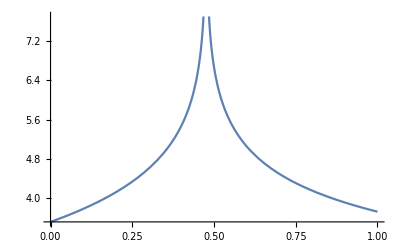

```mathematica
Plot[eK,{t,0,1}]
```

```mathematica
i=2;
j=2;
tmid=0.476256596615783;
{r,z}={Subscript[sx, i][t],Subscript[sy, i][t]};
{rp,zp}={Subscript[sx, j][t],Subscript[sy, j][t]}/.t->tmid;
{dr,dz}={Subscript[sx, i]'[t],Subscript[sy, i]'[t]};
J=√(dr^2+dz^2);
arc=NIntegrate[J,{t,0,1},PrecisionGoal->15,WorkingPrecision->15];
xi[g_?NumberQ]:=NIntegrate[J,{t,0,g},PrecisionGoal->15]/arc
a=rp^2+r^2+(zp-z)^2;
b=2 rp r;
m=2 b/(a+b);
eE=EllipticE[m];
eK=EllipticK[m];
N0=(1-xi[t])(1-2xi[t]) ;
N1=4(xi[t])(1-xi[t]) ;
N2=(xi[t])(2xi[t]-1) ;
SetOptions[NIntegrate,WorkingPrecision->14,PrecisionGoal->6];
NIntegrate[(r  J)/(π √(a+b))N0 eK  ,{t,0,tmid-0.0001}]+NIntegrate[(r  J)/(π √(a+b))N0 eK  ,{t,tmid+0.0001,1}]//NumberForm[#,{14,14}]&
NIntegrate[(r  J)/(π √(a+b))N1 eK  ,{t,0,tmid-0.00000001}]+NIntegrate[(r  J)/(π √(a+b))N1 eK  ,{t,tmid+0.00000001,1}]//NumberForm[#,{14,14}]&
NIntegrate[(r  J)/(π √(a+b))N2 eK  ,{t,0,tmid-0.00000001}]+NIntegrate[(r  J)/(π √(a+b))N2 eK  ,{t,tmid+0.00000001,1}]//NumberForm[#,{14,14}]&
```

```mathematica
SetOptions[NIntegrate,WorkingPrecision->14,PrecisionGoal->6];
NIntegrate[N0/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK) ,{t,0,tmid-0.0001}]+NIntegrate[N0/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK) ,{t,tmid+0.0001,1}]//NumberForm[#,{14,14}]&
NIntegrate[(r  J)/(π √(a+b))N1 eK  ,{t,0,tmid-0.00000001}]+NIntegrate[(r  J)/(π √(a+b))N1 eK  ,{t,tmid+0.00000001,1}]//NumberForm[#,{14,14}]&
NIntegrate[(r  J)/(π √(a+b))N2 eK  ,{t,0,tmid-0.00000001}]+NIntegrate[(r  J)/(π √(a+b))N2 eK  ,{t,tmid+0.00000001,1}]//NumberForm[#,{14,14}]&
```

-0.00144811112911

0.17523288163059

0.03919094518059

```mathematica
SetOptions[NIntegrate,WorkingPrecision->14,PrecisionGoal->5];
{NIntegrate[N0/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK),{t,0,1}],
NIntegrate[N1/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK),{t,0,1}],
NIntegrate[N2/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK),{t,0,1}]}//NumberForm[#,{14,14}]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.47653960961986}. NIntegrate obtained -0.062879095626724 and 6.7697506069113×10^-6 for the integral and error estimates.

{-0.00144811137588,-0.06287909562672,-0.03004187320642}

```mathematica
{r,z}={Subscript[sx, i][t],Subscript[sy, i][t]};
{rp,zp}={Subscript[sx, j][t],Subscript[sy, j][t]}/.t->1;
{dr,dz}={Subscript[sx, i]'[t],Subscript[sy, i]'[t]};
J=√(dr^2+dz^2);
arc=NIntegrate[J,{t,0,1},PrecisionGoal->15,WorkingPrecision->15];
xi[g_?NumberQ]:=NIntegrate[J,{t,0,g},PrecisionGoal->15]/arc
a=rp^2+r^2+(zp-z)^2;
b=2 rp r;
m=2 b/(a+b);
eE=EllipticE[m];
eK=EllipticK[m];
N0=(1-xi[t])(1-2xi[t]) ;
N1=4(xi[t])(1-xi[t]) ;
N2=(xi[t])(2xi[t]-1) ;
SetOptions[NIntegrate,WorkingPrecision->14,PrecisionGoal->5];
{NIntegrate[(r  J)/(π √(a+b))N0 eK  ,{t,0,1}],
NIntegrate[(r  J)/(π √(a+b))N1 eK  ,{t,0,1}],
NIntegrate[(r  J)/(π √(a+b))N2 eK  ,{t,0,1}]}//NumberForm[Transpose@{#},{14,14}]&
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.47653960961986}. NIntegrate obtained 0.17523293728248 and 0.000034392043524265 for the integral and error estimates.

{0.03033246192184,0.17523293728248,0.03919100377272}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.47653960961986}. NIntegrate obtained -0.062879095626724 and 6.7697506069113×10^-6 for the integral and error estimates.

{-0.00144811137588,-0.06287909562672,-0.03004187320642}

{{0.01945566219378},{0.12601337058088},{0.05245982097042}}

0.03033240105032

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.47653960961986}. NIntegrate obtained 0.17523293728248 and 0.000034392043524265 for the integral and error estimates.

0.17523293728248

0.03919100377272

```mathematica
0.476256596615783
```

0.17460913139336

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.04037034126692

```mathematica
SetOptions[NIntegrate,WorkingPrecision->14,PrecisionGoal->5];
NIntegrate[N0/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK),{t,0,1}]//NumberForm[#,{14,14}]&//Quiet
NIntegrate[N1/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK),{t,0,1}]//NumberForm[#,{14,14}]&
NIntegrate[N2/(π √(a+b))  (((dr (zp - z)-dz (rp - r))/(a-b)r -dz/2)eE +dz/2 eK),{t,0,1}]//NumberForm[#,{14,14}]&
```

-0.00381980356462

-0.06933783162583

-0.03634043663999

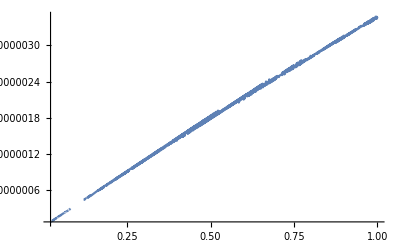

NIntegrate[((r J) eK)/(π √(a+b))]

0.218596

0.

0.446899

NIntegrate[J,{t,0,g}]

0.446899

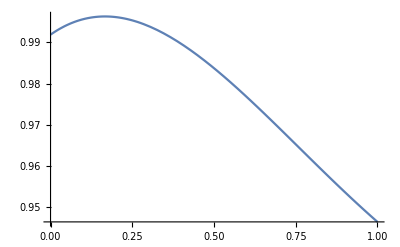

```mathematica
Log[1-m]*t;
Plot[Evaluate@Abs@%,{t,0,0.0000001},PlotRange->All,WorkingPrecision->MachinePrecision]
```

```mathematica
{r,z}/.t->1
{rp,zp}
```

{0.917393,0.917393}

{0.615279,0.726817}

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
GaussianQuadratureWeights[15,0.,1.,15]//MatrixForm
```

(0.00600374 | 0.0153766
0.0313633 | 0.035183
0.0758967 | 0.0535796
0.137791 | 0.0697853
0.214514 | 0.0831346
0.302924 | 0.0930805
0.399403 | 0.0992157
0.5 | 0.101289
0.600597 | 0.0992157
0.697076 | 0.0930805
0.785486 | 0.0831346
0.862209 | 0.0697853
0.924103 | 0.0535796
0.968637 | 0.035183
0.993996 | 0.0153766)

```mathematica
Integrate[ Log[x],{x,0,1}]
```

-1/4